```mathematica
f1/.input
f2/.input
f3/.input
f4/.input
```

-0.9 Cos[θ1]+1.18093 t2 Cos[θ1]+0.227617 Cos[θ1] Cos[θ2]+0.7 Sin[θ1]-1.82093 t2 Sin[θ1]+0.42 Cos[θ2] Sin[θ1]-0.42 Cos[θ1] Sin[θ2]+0.147617 Sin[θ1] Sin[θ2]

1.37237 Cos[θ2]-3.18663 t1 Cos[θ2]+0.147617 Cos[θ1] Cos[θ2]+0.42 Cos[θ2] Sin[θ1]-0.444 Sin[θ2]+2.06663 t1 Sin[θ2]-0.42 Cos[θ1] Sin[θ2]+0.227617 Sin[θ1] Sin[θ2]

-0.9+7 t1-3.36 t2-0.147617 Cos[θ2]-0.227617 Sin[θ2]

0.171627-5.88 t1+4. t2-0.227617 Cos[θ1]-0.147617 Sin[θ1]

```mathematica
ar1=Numerator[Together[solvetrig2[(Numerator[Together[(f4/.input)/.NSolve[(f3/.input)==0,t2][[1]]]]),
(Numerator[Together[(f1/.input)/.NSolve[(f3/.input)==0,t2][[1]]]]),θ2][[2,1]]]]//Factor
```

0.792763 (9.23628 Cos[θ1]^2-53.3914 t1 Cos[θ1]^2+72.7865 t1^2 Cos[θ1]^2+3.92617 Cos[θ1]^3-13.506 t1 Cos[θ1]^3+1. Cos[θ1]^4+11.98 Cos[θ1] Sin[θ1]-69.252 t1 Cos[θ1] Sin[θ1]+94.4087 t1^2 Cos[θ1] Sin[θ1]+9.88924 Cos[θ1]^2 Sin[θ1]-26.2773 t1 Cos[θ1]^2 Sin[θ1]+0.957996 Cos[θ1]^3 Sin[θ1]+3.88472 Sin[θ1]^2-22.4561 t1 Sin[θ1]^2+30.6135 t1^2 Sin[θ1]^2+7.873 Cos[θ1] Sin[θ1]^2-17.0417 t1 Cos[θ1] Sin[θ1]^2+1.13227 Cos[θ1]^2 Sin[θ1]^2+2.01748 Sin[θ1]^3-3.68402 t1 Sin[θ1]^3+1.35091 Cos[θ1] Sin[θ1]^3+0.484298 Sin[θ1]^4)

```mathematica
ar2=Numerator[Together[solvetrig2[(Numerator[Together[(f4/.input)/.NSolve[(f3/.input)==0,t2][[1]]]]),
(Numerator[Together[(f2/.input)/.NSolve[(f3/.input)==0,t2][[1]]]]),θ2][[2,1]]]]//Factor
```

57.7024 (0.0170697-0.191756 t1+0.799486 t1^2-1.46707 t1^3+1. t1^4+0.0158921 Cos[θ1]-0.137996 t1 Cos[θ1]+0.394222 t1^2 Cos[θ1]-0.371114 t1^3 Cos[θ1]+0.00661143 Cos[θ1]^2-0.0390295 t1 Cos[θ1]^2+0.0567781 t1^2 Cos[θ1]^2+0.00139933 Cos[θ1]^3-0.00414658 t1 Cos[θ1]^3+0.000118262 Cos[θ1]^4+0.0144657 Sin[θ1]-0.112175 t1 Sin[θ1]+0.286585 t1^2 Sin[θ1]-0.240679 t1^3 Sin[θ1]+0.00765593 Cos[θ1] Sin[θ1]-0.0398722 t1 Cos[θ1] Sin[θ1]+0.0511663 t1^2 Cos[θ1] Sin[θ1]+0.00145887 Cos[θ1]^2 Sin[θ1]-0.00389653 t1 Cos[θ1]^2 Sin[θ1]+0.000113294 Cos[θ1]^3 Sin[θ1]+0.00549613 Sin[θ1]^2-0.027502 t1 Sin[θ1]^2+0.0339218 t1^2 Sin[θ1]^2+0.0018021 Cos[θ1] Sin[θ1]^2-0.00439025 t1 Cos[θ1] Sin[θ1]^2+0.000133904 Cos[θ1]^2 Sin[θ1]^2+0.000936821 Sin[θ1]^3-0.00233942 t1 Sin[θ1]^3+0.000159761 Cos[θ1] Sin[θ1]^3+0.0000572739 Sin[θ1]^4)

```mathematica
{θ1->-0.9954539024686871,θ2->1.249745768690173,t1->0.49417816739482673,t2->0.6835352103847449}
```

```mathematica
g1/.input
g2/.input
```

(0.227617 Cos[θ1]+0.147617 Sin[θ1]) (-0.101523+0.0738083 Cos[θ1]+0.113808 Cos[θ2]-0.113808 Sin[θ1]-0.0738083 Sin[θ2])

-(-0.101523+0.0738083 Cos[θ1]+0.113808 Cos[θ2]-0.113808 Sin[θ1]-0.0738083 Sin[θ2]) (0.147617 Cos[θ2]+0.227617 Sin[θ2])

```mathematica
Solve[(0.2276166303929372 Cos[θ1]+0.14761663039293718 Sin[θ1])  ==0,θ1]
Solve[(0.14761663039293718 Cos[θ2]+0.2276166303929372 Sin[θ2]) ==0,θ2]
```

```mathematica
tmp2[[2]]/.input
```

```mathematica
Solve[(-0.14761663039293718 Cos[θ2]-0.2276166303929372 Sin[θ2])==0,θ2]
```

{{θ2→-0.575342},{θ2→2.56625}}

```mathematica
N[2.566250229263584*180/π]
N[-3.7169350779160024*180/π]
```

147.035

-212.965

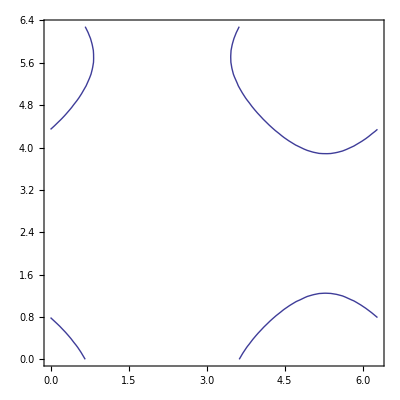

```mathematica
ContourPlot[(-0.10152332607858747+0.07380831519646859 Cos[θ1]+0.11380831519646858 Cos[θ2]-0.1138083151964686 Sin[θ1]-0.07380831519646859 Sin[θ2]) ==0,{θ1,0,2π},{θ2,0,2π}]
```

```mathematica
solt/.input/.{θ1->3.32,θ2->2.163}{{3.32,2.163}}
```

{t1→0.156587,t2→0.138967}

```mathematica
g1/.input/.(solt/.input/.{θ1->3.32,θ2->2.163})/.{θ1->3.32,θ2->2.163}
g2/.input/.(solt/.input/.{θ1->3.32,θ2->2.163})/.{θ1->3.32,θ2->2.163}
```

0.0697383

0.0296731